```mathematica
Save["渦電流とドロネー図eil51_関数変数データ","Global`*"]
```

```mathematica
Clear["Global`*"]
```

```mathematica
Get["渦電流とドロネー図eil51_関数変数データ"];
```

SetDelayed::write: {{61,133,140,132,92,125,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,«90»},{61,92,116,108,64,105,104,137,67,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,35,70,34,36,138,99,66,69,83,120,139,25,117,«76»},{92,116,108,64,105,104,137,67,136,106,52,122,118,46,29,53,127,98,101,109,63,130,121,102,110,119,107,82,54,70,34,138,99,66,83,120,139,25,117,40,100,103,14,123,32,26,95,80,71,50,«62»},«4»,{92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,30,124,88,87,111,2,20,77,8,84,96,9,5,3,28,4,49,10,22,19,7,21,37,79,18,17,1,6,57},{92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,124,88,87,111,77,84,96,49,37,79}}[PartLoop_,Rank_]のタグListはProtectedです．

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[GraphList[[i]]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
GreedyDirectedPartLoop[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* （新）Greedyを使った枝のランクを入力とした有向部分巡回路の構築(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

```mathematica
OutEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Join[Subsets[OutVertex[PartLoop],{2}],Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]](* PartLoopの頂点を使う枝を含む、PartLoopよりも外側の枝をランク順に出力 *)
```

```mathematica
EdgeRulesLine[LineList_]:=Table[i[[1]]-> i[[2]],{i,ToExpression[StringDelete[ToString[LineList],{"Line[","]"}]]}](* Edge Rules list from Line list: Lineのリストから枝の規則のリストを出力 *)
```

```mathematica
EdgeRulesMesh[mesh_]:=EdgeRulesLine[MeshCells[mesh,1]](* Edge Rules list from Mesh: MeshRegionのリストから枝の規則を出力 *)
```

```mathematica
InVertex[PartLoop_]:=DelEleList[Range[Length[Pin]],Join[VertexList[PartLoop],OutVertex[PartLoop]]](* PartLoopの内側の頂点 *)
```

```mathematica
InEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Subsets[InVertex[PartLoop],{2}]]](* PartLoopよりも内側の枝をランク順に出力 *)
```

### 渦電流の計算

```mathematica
Pin=Drop[Drop[Import["eil51.tsp","Table"],6],-1][[All,2;;3]](*Point input*)
```

{{37,52},{49,49},{52,64},{20,26},{40,30},{21,47},{17,63},{31,62},{52,33},{51,21},{42,41},{31,32},{5,25},{12,42},{36,16},{52,41},{27,23},{17,33},{13,13},{57,58},{62,42},{42,57},{16,57},{8,52},{7,38},{27,68},{30,48},{43,67},{58,48},{58,27},{37,69},{38,46},{46,10},{61,33},{62,63},{63,69},{32,22},{45,35},{59,15},{5,6},{10,17},{21,10},{5,64},{30,15},{39,10},{32,39},{25,32},{25,55},{48,28},{56,37},{30,40}}

```mathematica
GOrigin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];(* Ginの元のグラフ *)
```

```mathematica
PDOrigin=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[GOrigin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[GOrigin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[GOrigin]]}];(* Point Distance Origin *)
```

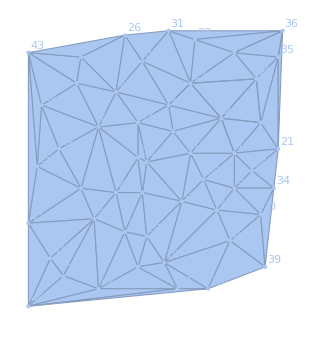

{40→19,19→41,41→40,40→42,42→19,19→4,4→41,41→13,13→40,13→4,4→18,18→13,4→47,47→18,18→25,25→13,42→4,17→42,42→44,44→17,42→45,45→44,37→44,44→15,15→37,37→17,47→17,17→12,12→47,4→17,37→12,47→6,6→18,12→5,5→46,46→12,40→45,51→47,12→51,25→14,14→24,24→25,18→14,23→24,24→6,6→23,24→43,43→25,43→23,23→7,7→43,23→48,48→7,7→26,26→43,14→6,43→13,27→6,6→51,51→27,51→46,46→27,48→26,48→8,8→26,48→1,1→8,27→1,48→27,48→6,8→31,31→26,46→32,32→27,37→5,15→45,45→33,33→15,40→33,5→15,15→49,49→5,5→38,38→11,11→5,49→38,16→11,38→16,11→46,10→15,33→10,11→32,10→39,39→30,30→10,33→39,39→34,34→30,30→49,49→10,49→9,9→38,30→9,50→34,34→21,21→50,50→9,9→34,9→16,50→16,1→32,32→2,2→1,11→2,2→22,22→1,31→22,22→28,28→31,8→22,3→28,22→3,28→36,36→31,2→20,20→22,16→21,21→29,29→16,21→35,35→29,29→20,2→29,3→20,20→35,35→3,35→36,36→3,21→36,2→16}

```mathematica
DelaunayMesh[Pin];
HighlightMesh[%,Labeled[0,"Index"]]
Ruleg=EdgeRulesMesh[%]
```

```mathematica
Ruleg={19->40,19->41,40->41,40->42,19->42,4->19,4->41,13->41,13->40,4->13,4->18,13->18,4->47,18->47,18->25,13->25,4->42,17->42,42->44,17->44,42->45,44->45,37->44,15->44,15->37,17->37,17->47,12->17,12->47,4->17,12->37,6->47,6->18,5->12,5->46,12->46,40->45,47->51,12->51,14->25,14->24,24->25,14->18,23->24,6->24,6->23,24->43,25->43,23->43,7->23,7->43,23->48,7->48,7->26,26->43,6->14,13->43,6->27,6->51,27->51,46->51,27->46,26->48,8->48,8->26,1->48,1->8,1->27,27->48,6->48,8->31,26->31,32->46,27->32,5->37,15->45,33->45,15->33,33->40,5->15,15->49,5->49,5->38,11->38,5->11,38->49,11->16,16->38,11->46,10->15,10->33,11->32,10->39,30->39,10->30,33->39,34->39,30->34,30->49,10->49,9->49,9->38,9->30,34->50,21->34,21->50,9->50,9->34,9->16,16->50,1->32,2->32,1->2,2->11,2->22,1->22,22->31,22->28,28->31,8->22,3->28,3->22,28->36,31->36,2->20,20->22,16->21,21->29,16->29,21->35,29->35,20->29,2->29,3->20,20->35,3->35,35->36,3->36,21->36,2->16};
```

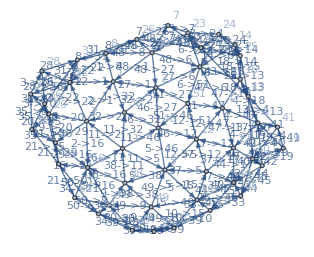

```mathematica
Gin=Graph[Ruleg,VertexLabels->"Name",EdgeLabels->"Name"](*Ggraph input*)
```

```mathematica
FundLoop=FindFundamentalCycles[UndirectedGraph[Gin]];
```

```mathematica
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
```

```mathematica
RuleRevFundLoop=Table[EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],{i,Length[FundLoop]}];
```

```mathematica
h=Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[Gin]}
],
{j,Length[FundLoop]}] ;(* 検算済 *)
```

```mathematica
PD=PDDelaunay=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
```

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]//N].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{-0.654196,-3.20093,4.09324,3.7544,-3.37937,-0.832636,2.2142,-5.07997,7.62543,-2.9511,5.62224,3.85149,-2.91763,11.4242,6.0351,4.41517,1.33071,-1.37526,1.9539,5.04144,2.47391,1.99951,-4.67137,-5.75939,12.3478,5.40614,-6.70909,-2.2581,18.5157,-7.37184,2.96783,-18.9157,-3.65678,17.461,-23.9011,13.3396,4.161,-29.7987,-21.9275,-9.9807,-2.99811,-10.103,3.50312,-1.92314,11.3055,35.7928,-6.12381,-1.49767,2.94439,5.99167,-3.18364,34.6687,-33.9573,-24.782,12.2418,-3.47947,1.48765,28.0031,2.12878,-30.2314,40.2314,30.8246,33.6613,55.273,-4.83234,-22.2704,-48.3573,-13.4684,-15.3893,17.3514,-9.24166,8.19486,8.27811,29.3309,8.64518,-0.753295,3.88209,-0.0961597,4.45748,14.9826,-0.278181,-18.606,12.4903,-3.26444,-3.92843,-5.26661,7.28937,-7.02771,36.112,2.18925,2.83566,73.9626,-1.52636,-2.36922,9.63092,5.60007,6.44292,-18.5169,-18.3896,-11.8037,17.0085,-17.5158,-12.1275,-30.4382,50.535,-30.5002,13.0778,56.0134,-20.5387,-13.1398,4.39229,57.3021,-57.7689,-102.121,-103.703,49.5427,21.9479,-34.5123,14.6289,20.9897,23.0154,-42.4926,-26.1258,24.7555,-138.399,33.3035,28.9102,11.3706,-36.9366,51.9055,-62.2269,127.29,141.21,-3.77373,-48.1862,39.5728,26.3734,22.1615,46.6694,113.842}

```mathematica
hrth=h.r.Transpose[h]//N;
```

```mathematica
Curr=Transpose[h].Inverse[hrth,Method->"CofactorExpansion"].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

General::munfl: -(2.80878×10^-302)/(7.3049×10^8)は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

Inverse::sing: 行列{{43.7353,21.,-7.2111,21.,0.,21.,0.,0.,0.,0.,-7.2111,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-7.2111,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«40»},«49»,«40»}は特異行列です．

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1},138,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.1.{-42,-5911/2,86,53/2,-40}
 |  |  |  |

```mathematica
Curr=Transpose[h].Inverse[hrth,Method->"OneStepRowReduction"].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{-0.654196,-3.20093,4.09324,3.7544,-3.37937,-0.832636,2.2142,-5.07997,7.62543,-2.9511,5.62224,3.85149,-2.91763,11.4242,6.0351,4.41517,1.33071,-1.37526,1.9539,5.04144,2.47391,1.99951,-4.67137,-5.75939,12.3478,5.40614,-6.70909,-2.2581,18.5157,-7.37184,2.96783,-18.9157,-3.65678,17.461,-23.9011,13.3396,4.161,-29.7987,-21.9275,-9.9807,-2.99811,-10.103,3.50312,-1.92314,11.3055,35.7928,-6.12381,-1.49767,2.94439,5.99167,-3.18364,34.6687,-33.9573,-24.782,12.2418,-3.47947,1.48765,28.0031,2.12878,-30.2314,40.2314,30.8246,33.6613,55.273,-4.83234,-22.2704,-48.3573,-13.4684,-15.3893,17.3514,-9.24166,8.19486,8.27811,29.3309,8.64518,-0.753295,3.88209,-0.0961597,4.45748,14.9826,-0.278181,-18.606,12.4903,-3.26444,-3.92843,-5.26661,7.28937,-7.02771,36.112,2.18925,2.83566,73.9626,-1.52636,-2.36922,9.63092,5.60007,6.44292,-18.5169,-18.3896,-11.8037,17.0085,-17.5158,-12.1275,-30.4382,50.535,-30.5002,13.0778,56.0134,-20.5387,-13.1398,4.39229,57.3021,-57.7689,-102.121,-103.703,49.5427,21.9479,-34.5123,14.6289,20.9897,23.0154,-42.4926,-26.1258,24.7555,-138.399,33.3035,28.9102,11.3706,-36.9366,51.9055,-62.2269,127.29,141.21,-3.77373,-48.1862,39.5728,26.3734,22.1615,46.6694,113.842}

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h],Method->"CofactorExpansion"].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

$Aborted

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h],Method->"OneStepRowReduction"].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

$Aborted

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h],Method->"DivisionFreeRowReduction"].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

$Aborted

```mathematica
Curr={-0.6541956247817773,-3.2009321703626243,4.093244024841108,3.7544015706282146,-3.379372562195754,-0.8326360166149067,2.2142035858035523,-5.079972609400182,7.625432709565308,-2.951095737223746,5.6222417751152,3.8514900294895065,-2.9176320712821493,11.424238162588072,6.035096236578545,4.415174367829161,1.330710034701199,-1.3752568791836606,1.9538986948262624,5.041437820168312,2.4739085241128476,1.999514801809258,-4.671367134243298,-5.75939145777609,12.34777566929567,5.406136900114727,-6.70909372454008,-2.2580971338474405,18.515744239241346,-7.371835008774062,2.9678297620170806,-18.91574691249341,-3.656777753717376,17.461023541785217,-23.901116751535014,13.339551762006787,4.160995211269794,-29.79871464240461,-21.92748339085013,-9.980696762561886,-2.998114550124045,-10.102951150138015,3.5031159179178455,-1.9231424981493714,11.305499296548767,35.79278538924219,-6.123805194684168,-1.4976674811732562,2.944392166465598,5.991669879527756,-3.183638327401426,34.66865017432941,-33.957323237904944,-24.78201503097576,12.241813391801003,-3.4794662945199972,1.4876451844230696,28.00313984311378,2.128783934600392,-30.23138595403618,40.231401140191046,30.824599404516395,33.661308850095104,55.2730029000029,-4.832342203072027,-22.270390042709753,-48.35733438004256,-13.468389465369091,-15.38931393262998,17.351365637476075,-9.241655828096018,8.194861775753663,8.278106643180745,29.33085085989444,8.645176141407154,-0.753294675448857,3.882094258124525,-0.09615972854145118,4.457475577290156,14.982598058568431,-0.27818104191731674,-18.606003058230826,12.490290221459505,-3.2644447850828775,-3.928425096468622,-5.266614702924759,7.28937166468782,-7.0277092639154795,36.11197342104791,2.1892530796785925,2.8356644541923344,73.96259528230286,-1.526358273939242,-2.3692157895607715,9.630922564370241,5.600065109763809,6.442922625385345,-18.516942662094927,-18.389584758673532,-11.803692212823224,17.008544173387968,-17.5158295675331,-12.127496257352401,-30.438247142171114,50.53502322224198,-30.50020551275901,13.07784733772078,56.01340507693283,-20.53868025564338,-13.139805708308696,4.3922863702190185,57.30213743580819,-57.76892379496753,-102.12121672727721,-103.70333753017358,49.542655293222836,21.94792020567954,-34.512306767581116,14.628922201189408,20.98966655112838,23.015434089532885,-42.49257414801069,-26.125794879237656,24.755515608339813,-138.39889329837035,33.30352515099669,28.910227044905163,11.37056314639868,-36.936584499114765,51.90547832447099,-62.22686660026685,127.28997794071377,141.20969689546715,-3.7737326806681253,-48.18617318932141,39.57277758008442,26.373394155331965,22.161497976790983,46.66941430903646,113.84237843657532};(*最新*)
```

```mathematica
Curr={0.16554297128774115,-0.6445478745723762,-0.6316689775577641,0.4889979668370806,0.6817069805453208,0.20270207726068545,0.23191676242154372,1.0443000897085968,1.1702311914968317,-0.03204795532235738,-0.565996972897805,-0.6398964685591615,-0.35755636731662854,-0.14041972026963015,0.18981984631897109,-1.0724948802008667,0.16014797208515152,-0.39326278995881786,0.2645978374912298,-0.8493049632073622,0.6729922920175051,0.47492574212962024,2.454328693393829,-1.394695825548077,1.5876370940527462,1.7308724937394004,-0.2918406729937869,-0.16437041618997578,-0.26824981916492546,0.3608344837694095,0.47332842162185096,0.25678443441564536,0.7498833508669477,-1.6800268552441922,-1.5338420451907555,-0.8811712658542781,0.6945809745664203,-0.8012821453293278,-0.8395637756568644,1.6516573264981496,-1.087201047733707,-0.8773874215324786,0.5054102166393596,0.4097509804965448,-1.205779417541796,3.943516343925532,-1.0058420632464795,-0.10840512891622472,-0.23208331337452903,-0.16427787962032125,-0.031163606927061438,3.601570797183196,3.7393202020189182,-3.543878715471536,1.911682000232052,1.0698664954038022,-0.5341878877677573,-1.6832153839554724,-0.7825913473416704,0.3399061688515881,2.5262777479272014,1.9887029362109983,-2.9858444931842563,-4.605960740445277,0.0010806774431866284,2.8740883028713844,-5.803909246317149,4.274689708063286,-0.27470959267097644,-2.348464475772989,-2.3430319584758132,-2.4686355450761432,0.09482816326527566,2.025586755329857,-1.3375093160201683,-0.8264423352647534,-1.0160566734487924,-0.04557978001287899,-0.7838641989388357,-2.100298270224502,-1.1756130146183867,7.660291402676499,0.6110453771218991,3.008122007046918,-1.61966029311878,8.05533949107549,-1.384121601342164,3.364625230045281,0.4842547189804518,0.2456044088331526,-0.3019272078231151,-1.6923830020750263,1.06815841904028,0.27593664705528415,0.31008765892661416,1.452413884551635,-0.9478019665424582,2.7411422046425264,-4.206652530537946,-1.3219232789769317,-9.011442069618726,1.0715468768613912,-1.499661337766748,3.74543742970068,-3.6505170192293313,-0.848159361278471,-2.2900371377877757,3.707010277745026,8.022583390566833,-1.8487069841047392,-0.607240930634434,1.9392291167628022,1.2411658289258787,4.898767090069377,2.0355324157289596,-11.496173025681983,-8.1828649714497,-2.3134404178625325,-5.491100096995616,4.4604159718561665,1.1440027751607553,8.037470334696328,10.386632858620526,-1.9140457341554487,-2.664691949558324,9.274073017178022,0.34386184849225465,1.0238199282778466,3.238109240486923,3.301638262376134,2.382396800222823,1.4480637740978373,-8.491471881843562,3.399788153078343,-26.700089508781623,-9.278406458252286,4.826666034857517,-0.6212798490741123,3.4493202806072443,1.750697252180645,0.4443807008401581};
```

```mathematica
Curr={0.9905480551683543,-4.819452576454544,-5.058900982154395,4.369538590536631,4.985244401406659,1.1563398801204716,1.9679374681915998,7.910416090417338,9.644928909839512,0.9544929029756627,-1.8593637933253118,-5.721016092198806,-2.5208742985992734,-3.9726049330501514,4.132613315014022,-8.082268599558681,-0.17671141164179893,-4.25865107933672,0.48578753016208376,-11.642447540093201,4.4336329708026865,2.8948111313892313,23.799998302922422,-9.748527161602075,20.168264175792366,13.09276840868106,0.5607259296838774,-2.725783533343628,0.8872972031163607,0.47817925227864544,1.5337928314298939,-0.8116557538779485,5.317768575169092,-10.39169522759357,-9.291843603799704,-6.870520651427102,5.487731657191836,-5.857111852727138,-3.216481077369082,16.18685097564209,-8.363814849220752,-10.848969228649711,2.422619692318895,0.7669514319242161,-10.453152008673005,44.24454352393187,-7.201046197319836,1.388226462447721,-2.0199263103498275,-7.09742580060527,-2.741212754426904,38.400092601752206,36.40357228767935,-26.564933732647177,13.371526205172549,10.245655818740236,-2.7975674055237016,-22.884367852909612,-10.643640070811632,6.233824515938581,13.483408484969276,1.271296889018081,-38.25269181841244,-60.645092387258074,-3.3260543191519787,26.679241654450543,-48.69495502638466,23.390077534560028,12.430029893357391,-15.01515223156899,-4.591616361619332,-5.009822438559282,14.961699993990237,-19.429441616663638,-10.994827112980897,-7.303604884465468,-5.512570874918289,-2.6930487036539095,-5.8371076994337905,-21.279053126316676,-15.394758653187383,68.62722465360048,0.8316860702896047,26.691724882532405,-17.501491653199253,76.81868608032897,4.754906223022491,22.398554782022934,13.41277585718777,6.307377899200199,-0.1388452681737613,4.348494948832235,5.7961337446822245,0.029912400212839696,1.36678601735173,8.517784602524411,-14.343830747419485,35.64859073320186,-40.56074686049611,-13.331452393060392,-76.15895282718557,26.896720345484013,-6.249029744433148,39.134545727250924,-62.31490251415061,-37.028532485482344,1.8909094423045367,51.457026760780195,2.163326023049958,-3.996922684073148,30.965791091391505,-0.9231444295698648,19.676350935057414,66.70939356477416,-61.024117046262376,-52.016506189074825,-17.607403779886717,-25.4498256459814,9.150261204406217,19.8678080416447,15.413193543277941,29.122873507772553,-19.18689330710969,-18.058581375659085,-85.3528924895509,20.992712260051814,24.337821083049818,43.93538260483661,57.42307841822904,42.544948100604984,34.437989200403,-73.94328380517285,7.022811982510163,-0.9730405997266516,-33.375361544156576,-26.975372131290328,16.632203625561175,-16.587654320033565,37.200925377241205,93.2442993531562};
```

```mathematica
Gout=GDelaunay=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

### TSPの解

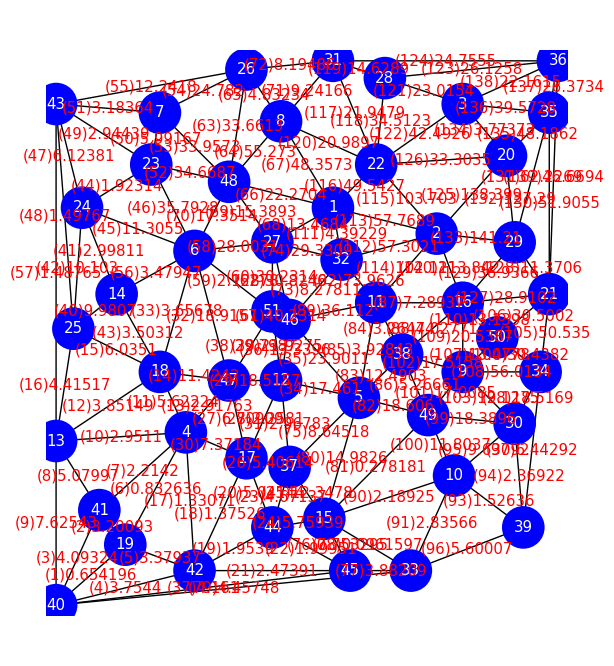

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

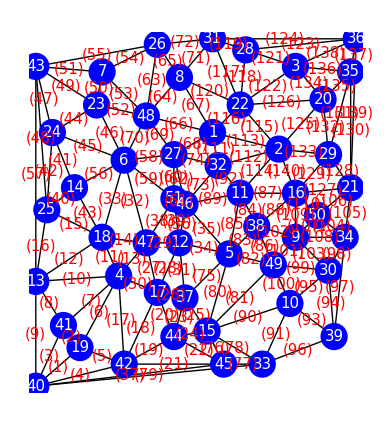

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")",FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

19→40 | 19→41 | 40→41 | 40→42 | 19→42 | 4→19 | 4→41 | 13→41 | 13→40 | 4→13
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

4→18 | 13→18 | 4→47 | 18→47 | 18→25 | 13→25 | 4→42 | 17→42 | 42→44 | 17→44
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

42→45 | 44→45 | 37→44 | 15→44 | 15→37 | 17→37 | 17→47 | 12→17 | 12→47 | 4→17
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30

12→37 | 6→47 | 6→18 | 5→12 | 5→46 | 12→46 | 40→45 | 47→51 | 12→51 | 14→25
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

14→24 | 24→25 | 14→18 | 23→24 | 6→24
41 | 42 | 43 | 44 | 45

```mathematica
PDCurrCost=Abs[PD/Curr ]
```

{16.2492,1.56204,2.95195,4.39282,2.52828,17.7326,6.07606,1.85709,2.49166,5.09414,1.35458,3.74458,2.67691,0.705715,1.85255,2.97903,12.0471,10.411,5.26928,1.69476,7.27594,5.14906,1.55845,1.05615,0.584,0.943191,1.37419,4.36157,0.324049,1.03309,3.38627,0.820701,3.98171,0.528007,0.503809,0.530083,8.22748,0.31659,0.367678,0.641551,3.59237,1.38926,2.93899,4.9055,1.232,0.312363,2.01987,17.4116,4.42822,1.0152,3.78234,0.265933,0.333174,0.451147,1.82658,2.95897,26.2159,0.32337,5.35599,0.264626,0.0555802,0.299097,0.390744,0.1668,1.49226,0.555415,0.241161,0.598606,0.55898,0.515479,0.997607,1.22636,1.11373,0.281145,1.30867,8.90515,1.80315,121.276,9.2417,0.971809,61.0055,0.443202,0.566125,2.05493,2.84601,1.44605,1.37186,1.31188,0.2824,7.22228,4.2611,0.0865725,6.55154,5.08252,0.957286,2.48718,2.81096,0.362274,0.546498,0.645203,0.376465,0.41563,0.699673,0.210364,0.17919,0.256072,0.432552,0.160676,0.389509,0.430513,1.38487,0.198976,0.214117,0.104093,0.102505,0.142727,0.592311,0.291197,0.432332,0.575666,0.412194,0.287263,0.769345,1.05027,0.0870064,0.451403,0.347624,0.63419,0.249605,0.404582,0.249477,0.0789526,0.0641272,2.06964,0.146745,0.253959,0.23064,0.545227,0.578934,0.0750512}

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{61,133,140,132,92,125,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}

```mathematica
FindShortestTour[Pin,PerformanceGoal->"Speed"]
Graphics[Line[Pin[[Last[%]]]]]
```

{31+34 √2+19 √5+5 √10+6 √13+5 √17+√26+2 √37+2 √41+2 √58+√61+3 √73+2 √82+2 √85+2 √89+√101+2 √106+2 √113+√145+2 √146+√173+√194,{1,32,11,38,5,49,10,39,33,45,15,37,17,44,42,19,40,41,13,25,14,18,4,47,12,46,51,27,6,48,23,24,43,7,26,8,31,28,3,36,35,20,29,21,34,30,9,50,16,2,22,1}}

-Graphics-

```mathematica
31+34 √2+19 √5+5 √10+6 √13+5 √17+√26+2 √37+2 √41+2 √58+√61+3 √73+2 √82+2 √85+2 √89+√101+2 √106+2 √113+√145+2 √146+√173+√194//N
```

428.982

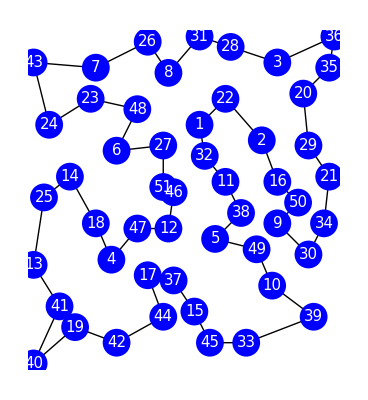

```mathematica
Graphics[{Line[Pin[[{1,32,11,38,5,49,10,39,33,45,15,37,17,44,42,19,40,41,13,25,14,18,4,47,12,46,51,27,6,48,23,24,43,7,26,8,31,28,3,36,35,20,29,21,34,30,9,50,16,2,22,1}]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

### 一貫した新しいgreedyを用いた解法4

```mathematica
GreedyDirectedPartLoop[PDCurrCostSort]
```

{2→29,29→20,20→2}

```mathematica
PartLoop1={2->29,29->20,20->2};
```

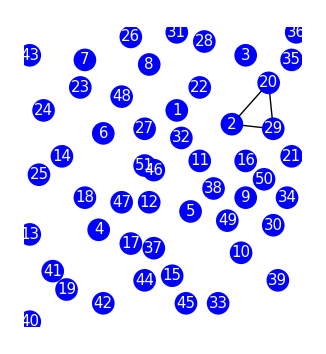

```mathematica
Graphics[{Table[Line[Pin[[VertexList[{i}]]]],{i,PartLoop1}],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
{20->3,3->22,22->2,2->20}
{2->16,16->29,29->20,20->2}
{2->29,29->20,20->2}
```

```mathematica
PartLoopProcess
```

{{2->29,29->20,20->2}}

```mathematica
OutEdgeRank[PartLoop1,PDCurrCostSort]
```

{61,140,92,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}

```mathematica
EdgeRules[Gout][[61]]
```

```mathematica
EdgeRules[Gout][[OutEdgeRank[PartLoop1,PDCurrCostSort]]]
```

{51→46,2→16,11→32,22→2,2→11,22→1,35→20,9→34,48→8,34→21,32→2,34→50,1→2,35→36,8→1,29→35,16→29,35→3,50→21,27→51,23→48,32→27,11→46,3→22,28→22,46→27,6→23,47→51,27→6,12→47,7→48,16→21,30→34,51→12,49→9,16→9,48→26,21→35,3→28,38→9,16→50,28→31,50→9,5→49,26→7,20→22,46→5,48→6,12→5,46→12,36→3,49→30,1→48,27→48,5→38,8→22,21→36,15→37,31→22,1→27,21→29,14→25,10→49,9→30,47→18,36→28,6→47,37→17,30→10,5→15,31→8,23→7,17→4,36→31,15→44,46→32,31→26,24→6,37→5,16→38,4→18,16→11,17→47,1→32,25→24,38→49,26→8,44→37,41→19,44→17,45→33,26→43,18→25,13→41,43→24,11→38,20→3,33→39,13→40,19→42,47→4,39→34,5→11,18→14,41→40,6→14,25→13,37→12,24→14,18→13,43→7,18→6,33→10,12→17,40→42,43→23,24→23,30→39,4→13,45→44,42→44,6→51,4→41,39→10,10→15,42→45,40→45,45→15,40→33,42→17,42→4,19→40,25→43,4→19,43→13,49→15,15→33}

```mathematica
OutEdgeRank1={51->46,2->16,11->32,22->2,2->11,22->1,35->20,9->34,48->8,34->21,32->2,34->50,1->2,35->36,8->1,29->35,16->29,35->3,50->21,27->51,23->48,32->27,11->46,3->22,28->22,46->27,6->23,47->51,27->6,12->47,7->48,16->21,30->34,51->12,49->9,16->9,48->26,21->35,3->28,38->9,16->50,28->31,50->9,5->49,26->7,20->22,46->5,48->6,12->5,46->12,36->3,49->30,1->48,27->48,5->38,8->22,21->36,15->37,31->22,1->27,21->29,14->25,10->49,9->30,47->18,36->28,6->47,37->17,30->10,5->15,31->8,23->7,17->4,36->31,15->44,46->32,31->26,24->6,37->5,16->38,4->18,16->11,17->47,1->32,25->24,38->49,26->8,44->37,41->19,44->17,45->33,26->43,18->25,13->41,43->24,11->38,20->3,33->39,13->40,19->42,47->4,39->34,5->11,18->14,41->40,6->14,25->13,37->12,24->14,18->13,43->7,18->6,33->10,12->17,40->42,43->23,24->23,30->39,4->13,45->44,42->44,6->51,4->41,39->10,10->15,42->45,40->45,45->15,40->33,42->17,42->4,19->40,25->43,4->19,43->13,49->15,15->33};
```

```mathematica
Gout=Gin=GOrigin; (* 閉路、枝、点をつなぎ合わせるときは、完全グラフを想定する必要がある *)
PD=PDOrigin;
```

```mathematica
InsertEdge[PartLoop1,51->46]
```

{29→20,20→2,51→46,2→51,29→46}

```mathematica
PartLoop2={29->20,20->2,51->46,2->51,29->46};
```

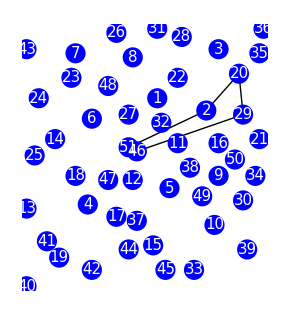

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop2]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
GreedyDirectedPartLoop[OutEdgeRank1]
```

{2→11,11→32,32→2}

```mathematica
PartLoop2=InsertVertex[PartLoop1,3]
```

{2→29,29→20,3→20,2→3}

```mathematica
InsertEdge[PartLoop1,2->16]
```

{29→20,20→2,2→16,16→29}

```mathematica
PartLoop2={29->20,20->2,2->16,16->29};
```

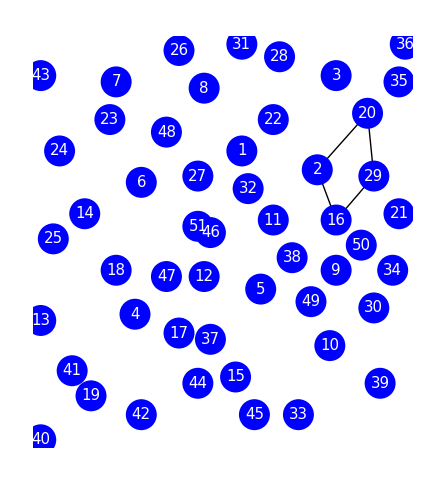

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop2]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
VertexSortFromLoopEdgeList[PartLoop2]
```

{2,20,29,16,2}

```mathematica
InsertEdge[PartLoop2,11->32]
```

{29→20,20→2,16→29,11→32,2→32,16→11}

```mathematica
PartLoop3={29->20,20->2,16->29,11->32,2->32,16->11};
```

```mathematica
VertexSortFromLoopEdgeList[PartLoop3]
```

{2,20,29,16,11,32,2}

```mathematica
InsertEdge[PartLoop3,22->2]
```

{29→20,20→2,16→29,11→32,16→11,22→2,22→32}

```mathematica
PartLoop4={29->20,20->2,16->29,11->32,16->11,22->2,22->32};
```

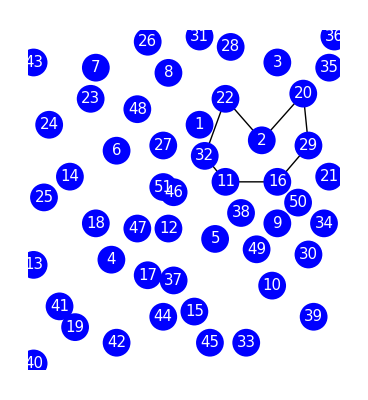

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop4]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
Gout=Gin=GDelaunay; (* 外側の点を挿入するときは再度ドロネー図を読み込む *)
PD=PDDelaunay;
```

#### 重み付け

```mathematica
PDWeight=PD*Table[1+i*0.1,{i,Length[PD]}][[Ordering[Ordering[PD]]]]
```

{126.499,5.5,154.663,94.0068,72.624,209.66,184.315,97.17,39.9,214.976,57.1183,73.5532,61.701,66.1105,44.7214,177.565,235.659,201.881,118.4,73.4784,36.,119.429,51.6888,38.3214,34.6133,29.5743,85.7418,104.398,7.2,57.8799,107.534,225.101,106.29,86.6637,149.316,19.0919,506.67,98.1134,66.9167,42.9009,64.622,196.499,120.459,99.0568,192.212,45.8394,66.7943,349.429,173.411,38.9297,150.52,87.5857,36.2039,46.9574,98.387,121.488,93.6,80.5929,139.101,11.2,7.82624,88.5076,178.88,89.4296,35.3344,68.0312,71.1376,67.723,75.7005,34.8827,90.3515,108.539,91.2735,42.8803,37.3352,24.1495,9.1,72.3038,617.92,107.746,57.6999,43.7049,19.799,24.8204,48.0755,58.6415,17.,92.1954,60.1684,74.3135,155.871,43.5412,18.,151.724,93.1174,193.605,166.619,25.4912,109.544,59.403,44.1816,52.4168,26.3044,44.8219,81.4985,62.482,14.1421,14.4,12.,14.7078,39.538,140.242,69.2682,127.562,128.625,20.5061,24.7,110.549,28.4605,157.08,43.6394,161.127,229.137,59.8,152.928,216.479,111.554,36.0555,94.0394,46.2,226.653,112.559,82.404,63.263,21.2132,113.564,40.1462,158.288,402.576,74.3328}

```mathematica
PDCurrCostSort
```

{61,133,140,132,92,125,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}

```mathematica
PDWeightCurrRank=Ordering[Abs[PDWeight/Curr]]
```

{61,108,60,29,116,135,133,109,92,140,132,130,53,107,125,110,117,113,115,114,46,98,36,74,67,104,137,83,105,64,89,2,54,121,119,70,106,103,87,77,82,124,112,52,129,101,25,136,62,58,102,39,66,128,118,38,131,122,127,40,75,69,34,68,100,9,63,26,14,99,35,50,126,24,138,80,65,15,120,84,30,55,139,123,111,95,71,11,47,73,23,86,93,32,85,27,88,72,21,20,134,45,12,8,42,13,5,41,4,97,33,76,90,43,96,56,31,3,16,28,51,44,91,49,22,19,57,94,59,10,7,37,79,18,17,1,81,48,6,78}

```mathematica
GreedyDirectedPartLoop[PDWeightCurrRank]
```

{20→2,2→29,29→20}

```mathematica
PartLoop1={20->2,2->29,29->20}
```

{20→2,2→29,29→20}

```mathematica
OutEdgeRank[PartLoop1,PDCurrCostSort]
```

{61,140,92,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}

```mathematica
EdgeRules[Gout][[{61,140,92,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}]]
```

{51→46,2→16,11→32,22→2,2→11,22→1,35→20,9→34,48→8,34→21,32→2,34→50,1→2,35→36,8→1,29→35,16→29,35→3,50→21,27→51,23→48,32→27,11→46,3→22,28→22,46→27,6→23,47→51,27→6,12→47,7→48,16→21,30→34,51→12,49→9,16→9,48→26,21→35,3→28,38→9,16→50,28→31,50→9,5→49,26→7,20→22,46→5,48→6,12→5,46→12,36→3,49→30,1→48,27→48,5→38,8→22,21→36,15→37,31→22,1→27,21→29,14→25,10→49,9→30,47→18,36→28,6→47,37→17,30→10,5→15,31→8,23→7,17→4,36→31,15→44,46→32,31→26,24→6,37→5,16→38,4→18,16→11,17→47,1→32,25→24,38→49,26→8,44→37,41→19,44→17,45→33,26→43,18→25,13→41,43→24,11→38,20→3,33→39,13→40,19→42,47→4,39→34,5→11,18→14,41→40,6→14,25→13,37→12,24→14,18→13,43→7,18→6,33→10,12→17,40→42,43→23,24→23,30→39,4→13,45→44,42→44,6→51,4→41,39→10,10→15,42→45,40→45,45→15,40→33,42→17,42→4,19→40,25→43,4→19,43→13,49→15,15→33}

#### PartLoopを含まず閉路を作る

```mathematica
EdgeNumList[DelEdgeVertexList[EdgeRules[Gout][[PDCurrCostSort]],VertexList[PartLoop1]]]
```

{61,92,116,108,64,105,104,137,67,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,35,70,34,36,138,99,66,69,83,120,139,25,117,68,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}

```mathematica
OutEdgeRank1={61,92,116,108,64,105,104,137,67,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,35,70,34,36,138,99,66,69,83,120,139,25,117,68,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78};
```

```mathematica
GreedyDirectedPartLoop[OutEdgeRank1]
```

{51→46,46→27,27→51}

```mathematica
Clear[OutLoop,OutEdgeRank]
```

```mathematica
OutLoop={PartLoop1};
OutEdgeRank={PDCurrCostSort};
For[j=1,j<8,j++,
OutEdgeRank=Append[OutEdgeRank,EdgeNumList[DelEdgeVertexList[EdgeRules[Gout][[OutEdgeRank[[j]]]],VertexList[OutLoop[[j]]]]]];
OutLoop=Append[OutLoop,GreedyDirectedPartLoop[OutEdgeRank[[j+1]]]]
]
```

```mathematica
OutEdgeRank=Append[OutEdgeRank,EdgeNumList[DelEdgeVertexList[EdgeRules[Gout][[OutEdgeRank[[8]]]],VertexList[OutLoop[[8]]]]]]
```

{{61,133,140,132,92,125,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78},{61,92,116,108,64,105,104,137,67,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,35,70,34,36,138,99,66,69,83,120,139,25,117,68,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78},{92,116,108,64,105,104,137,67,136,106,52,122,118,46,29,53,127,98,101,109,63,130,121,102,110,119,107,82,54,70,34,138,99,66,83,120,139,25,117,40,100,103,14,123,32,26,95,80,71,50,30,124,24,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78},{92,116,64,137,67,136,52,122,118,46,29,53,127,63,130,121,119,82,54,70,34,138,99,66,83,120,139,25,117,40,100,14,123,32,26,95,80,71,50,30,124,24,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,96,9,5,13,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78},{92,116,137,67,136,122,118,46,29,127,130,121,119,82,34,138,99,83,120,139,25,117,40,100,14,123,32,26,95,80,71,30,124,24,45,75,88,11,87,27,111,42,86,23,2,20,77,15,8,47,84,96,9,5,13,85,43,3,56,16,31,41,12,33,91,28,4,49,44,94,10,22,19,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78},{92,116,137,67,136,122,118,46,29,127,130,121,119,34,138,83,120,139,25,117,40,14,123,32,26,80,71,30,124,24,45,75,88,11,87,27,111,42,23,2,20,77,15,8,47,84,96,9,5,13,85,43,3,56,16,31,41,12,33,28,4,49,44,10,22,19,7,21,37,76,79,18,17,1,48,6,57,78},{92,116,137,67,136,122,118,46,29,127,130,121,119,138,120,139,117,40,14,123,32,71,30,124,45,88,11,87,27,111,42,2,20,77,15,8,47,84,96,9,5,13,43,3,56,16,41,12,33,28,4,49,44,10,22,19,7,21,37,79,18,17,1,48,6,57},{92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,30,124,88,87,111,2,20,77,8,84,96,9,5,3,28,4,49,10,22,19,7,21,37,79,18,17,1,6,57},{92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,124,88,87,111,77,84,96,49,37,79}}

```mathematica
OutLoop=Append[OutLoop,GreedyDirectedPartLoop[OutEdgeRank[[9]]]]
```

Part::partw: {92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,124,88,87,111,77,84,96,49,37,79}の部分28は存在しません．

Part::pkspec1: 式{92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,124,88,87,111,77,84,96,49,37,79}⟦28⟧は部分指定に使用できません．

FindCycle::graph: FindCycle[Graph[{11→32,22→1,35→36,8→1,35→3,3→22,28→22,16→21,21→35,28→31,16→38,16→11,45→33,33→39,43→23,40→45,{19→40,41→19,41→40,40→42,19→42,4→19,4→41,13→41,13→40,4→13,4→18,18→13,47→4,47→18,18→25,25→13,42→4,42→17,42→44,44→17,42→45,45→44,44→37,15→44,15→37,37→17,17→47,12→17,12→47,17→4,37→12,6→47,18→6,12→5,46→5,46→12,40→45,47→51,51→12,14→25,24→14,25→24,18→14,24→23,24→6,6→23,43→24,25→43,43→23,23→7,«90»}⟦«1»⟦28⟧⟧}],∞,All]の位置1にはグラフオブジェクトが想定されています．

EdgeRules::graph: EdgeRules[Graph[{11→32,«15»,{19→40,41→19,41→40,40→42,19→42,4→19,4→41,13→41,13→40,4→13,4→18,18→13,47→4,47→18,18→25,25→13,42→4,42→17,42→44,44→17,42→45,45→44,44→37,15→44,15→37,37→17,17→47,12→17,12→47,17→4,37→12,6→47,18→6,12→5,46→5,46→12,40→45,47→51,51→12,14→25,24→14,25→24,18→14,24→23,24→6,6→23,43→24,25→43,43→23,23→7,«90»}⟦{92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,124,88,87,111,77,84,96,49,37,79}⟦28⟧⟧}]]の位置1にはグラフオブジェクトが想定されています．

EdgeRules::graph: EdgeRules[∞]の位置1にはグラフオブジェクトが想定されています．

{{20→2,2→29,29→20},{51→46,46→27,27→51},{9→34,34→50,50→9},{48→26,26→7,7→48},{49→30,30→10,10→49},{5→15,15→37,37→5},{6→47,47→18,18→25,25→24,24→6},{17→4,4→13,13→41,41→19,19→42,42→44,44→17},EdgeRules[Graph[{11→32,22→1,35→36,8→1,35→3,3→22,28→22,16→21,21→35,28→31,16→38,16→11,45→33,33→39,43→23,40→45,{19→40,41→19,41→40,40→42,19→42,4→19,4→41,13→41,13→40,4→13,4→18,18→13,47→4,47→18,18→25,25→13,42→4,42→17,42→44,44→17,42→45,45→44,44→37,15→44,15→37,37→17,17→47,12→17,12→47,17→4,37→12,6→47,18→6,12→5,46→5,46→12,40→45,47→51,51→12,14→25,24→14,25→24,18→14,24→23,24→6,6→23,43→24,25→43,43→23,23→7,43→7,23→48,7→48,26→7,26→43,6→14,43→13,27→6,6→51,27→51,51→46,46→27,48→26,48→8,26→8,1→48,8→1,1→27,27→48,48→6,31→8,31→26,46→32,32→27,37→5,45→15,45→33,15→33,40→33,5→15,49→15,5→49,5→38,11→38,5→11,38→49,16→11,16→38,11→46,10→15,33→10,11→32,39→10,30→39,30→10,33→39,39→34,30→34,49→30,10→49,49→9,38→9,9→30,34→50,34→21,50→21,50→9,9→34,16→9,16→50,1→32,32→2,1→2,2→11,22→2,22→1,31→22,28→22,28→31,8→22,3→28,3→22,36→28,36→31,20→2,20→22,16→21,21→29,16→29,21→35,29→35,29→20,2→29,20→3,35→20,35→3,35→36,36→3,21→36,2→16}⟦{92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,124,88,87,111,77,84,96,49,37,79}⟦28⟧⟧}]]}

```mathematica
Length[{92,116,137,67,136,122,118,127,130,121,119,138,120,139,117,123,71,124,88,87,111,77,84,96,49,37,79}]
```

27

```mathematica
OutLoop
```

{{20→2,2→29,29→20},{51→46,46→27,27→51},{9→34,34→50,50→9},{48→26,26→7,7→48},{49→30,30→10,10→49},{5→15,15→37,37→5},{6→47,47→18,18→25,25→24,24→6},{17→4,4→13,13→41,41→19,19→42,42→44,44→17}}

```mathematica
Flatten[OutLoop]
```

{20→2,2→29,29→20,51→46,46→27,27→51,9→34,34→50,50→9,48→26,26→7,7→48,49→30,30→10,10→49,5→15,15→37,37→5,6→47,47→18,18→25,25→24,24→6}

```mathematica
line1=Table[Line[Pin[[VertexList[{i}]]]],{i,Flatten[OutLoop]}]
```

{Line[{{57,58},{49,49}}],Line[{{49,49},{58,48}}],Line[{{58,48},{57,58}}],Line[{{30,40},{32,39}}],Line[{{32,39},{30,48}}],Line[{{30,48},{30,40}}],Line[{{52,33},{61,33}}],Line[{{61,33},{56,37}}],Line[{{56,37},{52,33}}],Line[{{25,55},{27,68}}],Line[{{27,68},{17,63}}],Line[{{17,63},{25,55}}],Line[{{48,28},{58,27}}],Line[{{58,27},{51,21}}],Line[{{51,21},{48,28}}],Line[{{40,30},{36,16}}],Line[{{36,16},{32,22}}],Line[{{32,22},{40,30}}],Line[{{21,47},{25,32}}],Line[{{25,32},{17,33}}],Line[{{17,33},{7,38}}],Line[{{7,38},{8,52}}],Line[{{8,52},{21,47}}]}

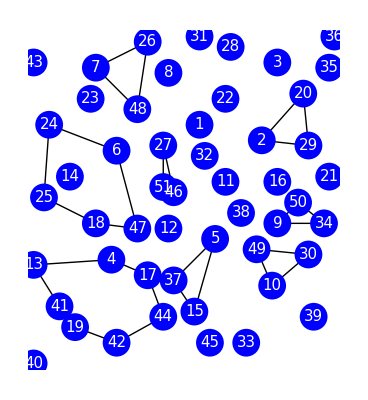

```mathematica
Graphics[{Table[Line[Pin[[VertexList[{i}]]]],{i,Flatten[OutLoop]}],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
Graphics[{Table[Line[Pin[[VertexList[{i}]]]],{i,Graphics[{Table[Line[Pin[[VertexList[{i}]]]],{i,{2->29,29->20,20->2,51->46,2->16,11->32,22->2,2->11,22->1,35->20,9->34,48->8,34->21,32->2,34->50,1->2,35->36,8->1,29->35,16->29,35->3,50->21,27->51,23->48,32->27,11->46,3->22,28->22,46->27,6->23,47->51,27->6,12->47,7->48,16->21,30->34,51->12,49->9,16->9,48->26,21->35,3->28,38->9,16->50,28->31,50->9,5->49,26->7,20->22,46->5,48->6,12->5,46->12,36->3,49->30,1->48,27->48,5->38,8->22}}],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]}],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

Table::iterb: 反復演算…は適正な範囲を持ちません．

-Graphics-

```mathematica
OutEdgeRank
```

{{61,92,116,108,64,105,104,137,67,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,35,70,34,36,138,99,66,69,83,120,139,25,117,68,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78},{NotFound,NotFound}}

```mathematica
OutLoop
```

{{2→29,29→20,20→2},EdgeRules[Graph[{{19→40,41→19,41→40,40→42,19→42,4→19,4→41,13→41,13→40,4→13,4→18,18→13,47→4,47→18,18→25,25→13,42→4,42→17,42→44,44→17,42→45,45→44,44→37,15→44,15→37,37→17,17→47,12→17,12→47,17→4,37→12,6→47,18→6,12→5,46→5,46→12,40→45,47→51,51→12,14→25,24→14,25→24,18→14,24→23,24→6,6→23,43→24,25→43,43→23,23→7,43→7,23→48,7→48,26→7,26→43,6→14,43→13,27→6,6→51,27→51,51→46,46→27,48→26,48→8,26→8,1→48,8→1,1→27,27→48,48→6,31→8,31→26,46→32,32→27,37→5,45→15,45→33,15→33,40→33,5→15,49→15,5→49,5→38,11→38,5→11,38→49,16→11,16→38,11→46,10→15,33→10,11→32,39→10,30→39,30→10,33→39,39→34,30→34,49→30,10→49,49→9,38→9,9→30,34→50,34→21,50→21,50→9,9→34,16→9,16→50,1→32,32→2,1→2,2→11,22→2,22→1,31→22,28→22,28→31,8→22,3→28,3→22,36→28,36→31,20→2,20→22,16→21,21→29,16→29,21→35,29→35,29→20,2→29,20→3,35→20,35→3,35→36,36→3,21→36,2→16}⟦NotFound⟧}]]}

```mathematica
OutLoop={PartLoop1}
```

{{2→29,29→20,20→2}}

```mathematica
OutEdgeRank={PDCurrCostSort}
```

{{61,133,140,132,92,125,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}}

```mathematica
OutEdgeRank[[1]]
```

{61,133,140,132,92,125,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}

```mathematica
OutEdgeRank
```

{{61,133,140,132,92,125,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}}

```mathematica
OutLoop
```

{{2→29,29→20,20→2},334,EdgeRules[Graph[{{19→40,41→19,41→40,40→42,19→42,4→19,4→41,13→41,13→40,4→13,4→18,18→13,47→4,47→18,18→25,25→13,42→4,42→17,42→44,44→17,42→45,45→44,44→37,15→44,15→37,37→17,17→47,12→17,12→47,17→4,80,1→32,32→2,1→2,2→11,22→2,22→1,31→22,28→22,28→31,8→22,3→28,3→22,36→28,36→31,20→2,20→22,16→21,21→29,16→29,21→35,29→35,29→20,2→29,20→3,35→20,35→3,35→36,36→3,21→36,2→16}⟦1⟧}]]}
 |  |  |  |

```mathematica
OutLoop[[2]]
```

EdgeRules[Graph[{{19→40,41→19,41→40,40→42,19→42,4→19,4→41,13→41,13→40,4→13,4→18,18→13,47→4,47→18,18→25,25→13,42→4,42→17,42→44,44→17,42→45,45→44,44→37,15→44,15→37,37→17,17→47,12→17,12→47,17→4,37→12,6→47,18→6,12→5,46→5,46→12,40→45,47→51,51→12,14→25,24→14,25→24,18→14,24→23,24→6,6→23,43→24,25→43,43→23,23→7,43→7,23→48,7→48,26→7,26→43,6→14,43→13,27→6,6→51,27→51,51→46,46→27,48→26,48→8,26→8,1→48,8→1,1→27,27→48,48→6,31→8,31→26,46→32,32→27,37→5,45→15,45→33,15→33,40→33,5→15,49→15,5→49,5→38,11→38,5→11,38→49,16→11,16→38,11→46,10→15,33→10,11→32,39→10,30→39,30→10,33→39,39→34,30→34,49→30,10→49,49→9,38→9,9→30,34→50,34→21,50→21,50→9,9→34,16→9,16→50,1→32,32→2,1→2,2→11,22→2,22→1,31→22,28→22,28→31,8→22,3→28,3→22,36→28,36→31,20→2,20→22,16→21,21→29,16→29,21→35,29→35,29→20,2→29,20→3,35→20,35→3,35→36,36→3,21→36,2→16}⟦NotFound⟧}]]

```mathematica
OutLoop[[3]]
```

EdgeRules[Graph[{{19→40,41→19,41→40,40→42,19→42,4→19,4→41,13→41,13→40,4→13,4→18,18→13,47→4,47→18,18→25,25→13,42→4,42→17,42→44,44→17,42→45,45→44,44→37,15→44,15→37,37→17,17→47,12→17,12→47,17→4,37→12,6→47,18→6,12→5,46→5,46→12,40→45,47→51,51→12,14→25,24→14,25→24,18→14,24→23,24→6,6→23,43→24,25→43,43→23,23→7,43→7,23→48,7→48,26→7,26→43,6→14,43→13,27→6,6→51,27→51,51→46,46→27,48→26,48→8,26→8,1→48,8→1,1→27,27→48,48→6,31→8,31→26,46→32,32→27,37→5,45→15,45→33,15→33,40→33,5→15,49→15,5→49,5→38,11→38,5→11,38→49,16→11,16→38,11→46,10→15,33→10,11→32,39→10,30→39,30→10,33→39,39→34,30→34,49→30,10→49,49→9,38→9,9→30,34→50,34→21,50→21,50→9,9→34,16→9,16→50,1→32,32→2,1→2,2→11,22→2,22→1,31→22,28→22,28→31,8→22,3→28,3→22,36→28,36→31,20→2,20→22,16→21,21→29,16→29,21→35,29→35,29→20,2→29,20→3,35→20,35→3,35→36,36→3,21→36,2→16}⟦{{61,92,116,108,64,105,104,137,67,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,35,70,34,36,138,99,66,69,83,120,139,25,117,68,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78},{NotFound,NotFound},{{}⟦1⟧,NotFound}}⟧}]]

```mathematica
OutEdgeRank[[3]]
```

{{}⟦1⟧,NotFound}